```mathematica
(* Free energy of the finite-N SU(N) matrix model *)
ϵ=0.00001;
FE[NC_,λ_]:=Module[{M,Res,pc,l,c1,c2},
M=Table[BesselI[j-i,(2NC)/λ]Exp[-(2NC)/λ],{j,1,NC},{i,1,NC}];
Res=Det[M];
l=1;
While[l<2 || (Abs[c1]+Abs[c2])/Abs[Res]>ϵ,
M=Table[BesselI[l+j-i,(2NC)/λ]Exp[-(2NC)/λ],{j,1,NC},{i,1,NC}];
c1=Det[M];
M=Table[BesselI[-l+j-i,(2NC)/λ]Exp[-(2NC)/λ],{j,1,NC},{i,1,NC}];
c2=Det[M];
Res+=c1 +c2;
l++;
];
-1/NC^2 Log[Res]
];
(* Free energy and its derivatives in the infinite-N limit - Gross-Witten result (with our change of normalization) *)
FGW[λ_]:=If[λ<2,-1/2 Log[λ/2]+3/4,2/λ-1/λ^2];
DFGW[λ_]:=If[λ<2,-1/(2λ),-2/λ^2+2/λ^3];
DDFGW[λ_]:=If[λ<2,1/(2 λ^2),4/λ^3-6/λ^4];
DDDFGW[λ_]:=If[λ<2,-1/λ^3,-12/λ^4+24/λ^5];
```

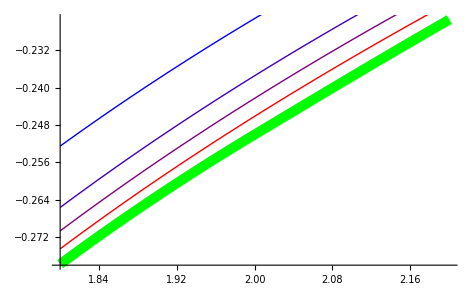

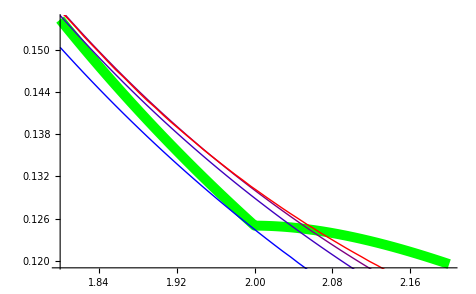

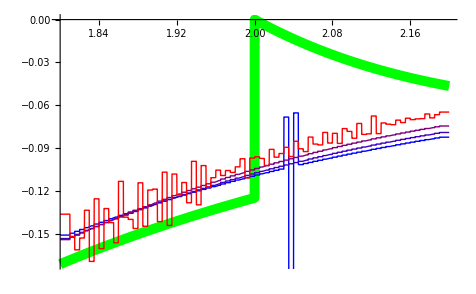

```mathematica
dλ=0.005;
λmin=1.8;
λmax=2.2;
NCs={4,6,8,12};
NCMax=Max[NCs];
NCMin=Min[NCs];
GrAs={Plot[DFGW[λ],{λ,λmin,λmax},PlotStyle->{RGBColor[0,1,0],Thickness[0.015]}]}; GrBs={Plot[DDFGW[λ],{λ,λmin,λmax},PlotStyle->{RGBColor[0,1,0],Thickness[0.015]}]};
 GrCs={Plot[DDDFGW[λ],{λ,λmin,λmax},PlotStyle->{RGBColor[0,1,0],Thickness[0.015]}]};
For[inc=1,inc≤Length[NCs],inc++,
NC0=NCs[[inc]];
ρ=(NC0-NCMin)/(NCMax-NCMin);
FET=Table[{λ,FE[NC0,λ]},{λ,λmin,λmax,dλ}];
FEI=Interpolation[FET];
DFEI[λ_]:=FEI'[λ];
DDFEI[λ_]:=FEI''[λ];
DDDFEI[λ_]:=FEI'''[λ];
GrA=Plot[ DFEI[λ],{λ,λmin,λmax},PlotStyle->{RGBColor[ρ,0,1-ρ]}];
GrB=Plot[ DDFEI[λ],{λ,λmin,λmax},PlotStyle->{RGBColor[ρ,0,1-ρ]}];
GrC=Plot[DDDFEI[λ],{λ,λmin,λmax},PlotStyle->{RGBColor[ρ,0,1-ρ]}];
AppendTo[GrAs,GrA];
AppendTo[GrBs,GrB];
AppendTo[GrCs,GrC];
(*Print[Show[GrA]];
Print[Show[GrB]];
Print[Show[GrC]];*)
];
Show[GrAs]
Show[GrBs]
Show[GrCs]
```

```mathematica
FullSimplify[D[FGW[λ],{λ,2}]]
```

Piecewise[{{1/(2 λ^2), λ<2}, {(-6+4 λ)/λ^4, True}}]

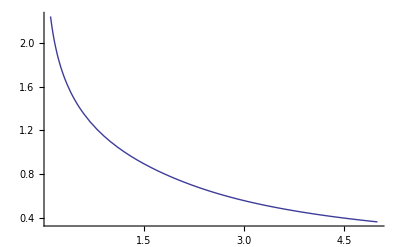

```mathematica
Plot[{FGW[λ],FGW[λ]},{λ,0.1,5}]
```

General::ivar: 0.000128356 is not a valid variable.

General::ivar: 0.128357 is not a valid variable.

General::ivar: 0.256585 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

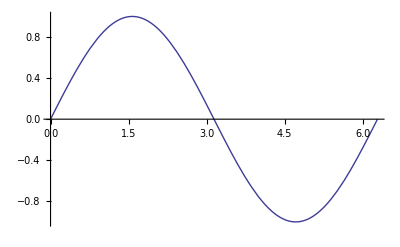

Derivative

```mathematica
Plot[{Sin[x],D[Sin[x],x]},{x,0,2π}]
Derivative
```